# Rescaled f(R)Canonical Scalar Field Inflation In The Presence Of A Chern-Simons Term.

## Hybrid Inflation With A Power-Law Chern-Simons Scalar Coupling Function.

## 1.Designation Of Scalar Functions, Equations Of Motion, Slow-Roll/Observed Indices.

We start by designating the scalar functions of the model. For simplicity, the Chern-Simons scalar coupling function obtains a power-law form along with the scalar potential. Compatibility is achieved for a quadratic potential but we shall keep it arbitrary for the time being so as to study the dependence of the observed indices, and especially the scalar spectral index ns on such exponent. The equations of motion are extracted by assuming the slow-roll condition is valid. Slow-roll indices along with observed indices are taken from arXiv:0412126.

Every parameter that ends with 1 is an auxiliary free parameter that needs to be designated later. With v and V the Chern-Simons coupling and the scalar potential are denoted while H is Hubble’s parameter and H2 the squared Hubble. Each parameter ending with dot implies time derivative for simplicity and Qt is an auxiliary function that depends on both the scalar field and the polarization of gravitational waves. Finally, indices ε1 through ε3 are the slow-roll indices of the model and ns, nt, r indicate the observed indices.

```mathematica
v[φ_]:=Λ1 (κ φ)^p
vdot[φ_]:=D[v[φ],φ]φdot[φ]
V[φ_]:=V1(κ φ)^n
H2[φ_]:=κ^2 V[φ]/(3α)
H[φ_]:=Sqrt[H2[φ]]
φdot[φ_]:=(-D[V[φ],φ])/(3H[φ])
Hdot[φ_]:=-κ^2/(2α)φdot[φ]^2
Qt[λ_,φ_]:=α/κ^2+2λ vdot[φ]H[φ]
ε1[φ_]:=(-Hdot[φ])/H2[φ]
ε2[φ_]:=ε1[φ]-D[V[φ],{φ,2}]/(κ^2 V[φ])
ε6[φ_]:=(D[Qt[1,φ],φ]φdot[φ])/(2H[φ]Qt[1,φ])+(D[Qt[-1,φ],φ]φdot[φ])/(2H[φ]Qt[-1,φ])
ns[φ_]:=1-2(2ε1[φ]+ε2[φ])
nt[φ_]:=-2(ε1[φ]+ε6[φ])
r[φ_]:=8Abs[ε1[φ]](α/Abs[κ^2 Qt[1,φ]]+α/Abs[κ^2 Qt[-1,φ]])
```

## 2. Extracting The Values Of The Scalar Field.

To study the inflationary era, one needs to insert as an input the value of the scalar field during the first horizon crossing to the observed indices. Such a value can be extracted by firstly finding the final value during the ending stage of the inflationary era by imposing that ε1 becomes of order O(1). Afterwards, by using the e-folding number N=∫ Hdt, the initial value can be extracted as a function of N and φf.

I use variable U to denote solutions hereafter while L is a random variable such that the initial value of the scalar field can be extracted.

```mathematica
U1=Solve[ε1[φ]==1,φ];
φf=φ/.U1[[2]]/.C[1]->0;
L1=Integrate[H[φ]/φdot[φ],φ]/.φ->φl;
L2=Integrate[H[φ]/φdot[φ],φ]/.φ->φk;
U2=Solve[N0==L1-L2,φk];
φi=φk/.U2[[2]]/.{C[1]->0,φl->φf};
```

## 3. Designation Of Free Parameters And Validity Of Approximations.

### 3.1. Derivation Of Observed Indices.

By assigning numerical values to the free parameters of the model, the initial value of the scalar field during the first horizon crossing is extracted. Subsequently, one can use such value as an input on the observed indices and derive results. Here, a blue shifted tensor spectral index (nt>0) can be achieved under the slow-roll assumption due to the presence of the Chern-Simons term in the initial gravitational action.

```mathematica
κ=1/Mp;Mp=1; Λ1=1;V1=Mp^4;N0=60.;n=0.999;p=2;α=0.0014;
φi/Mp//N
φf/Mp//N
ns[φ]/.φ->φi//N
nt[φ]/.φ->φi//N
r[φ]/.φ->φi//N
```

0.410525

0.0264311

0.963273

0.0082906

0.000169657

### 3.2. Observed Indices

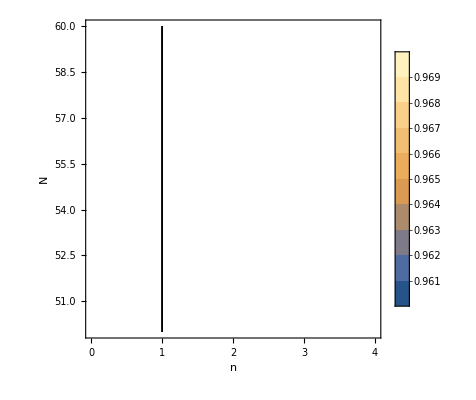

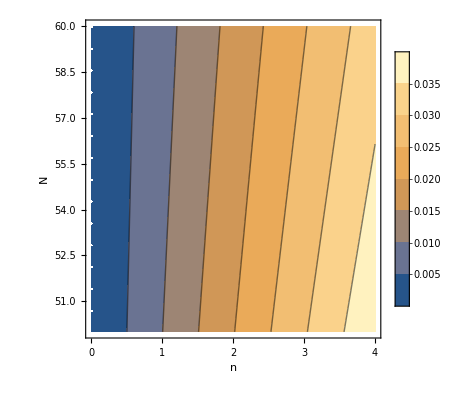

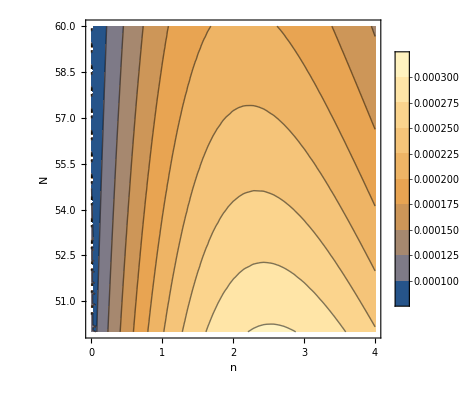

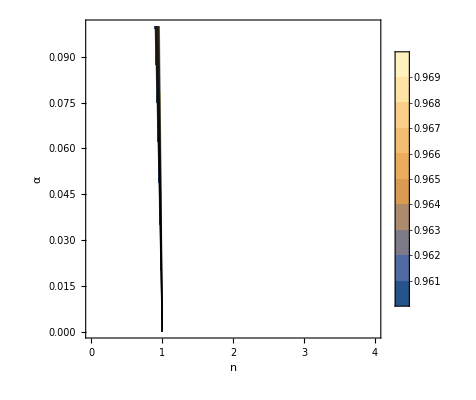

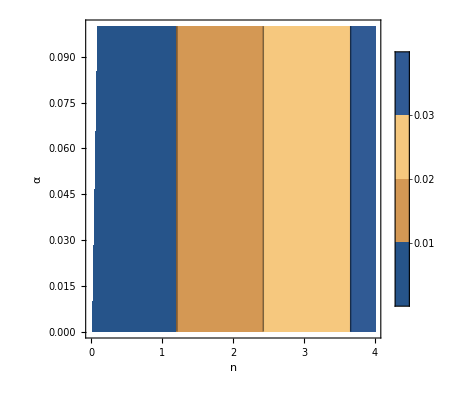

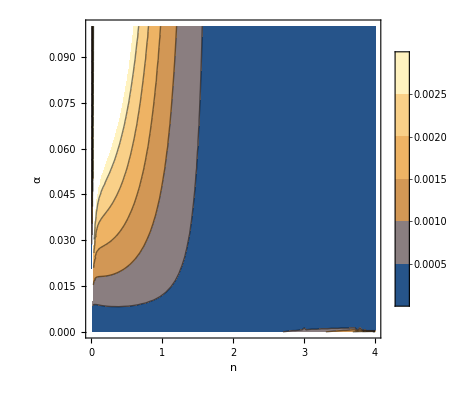

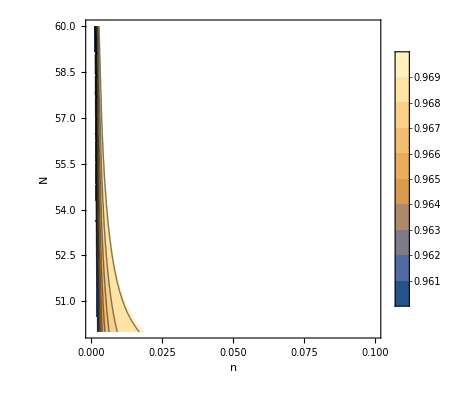

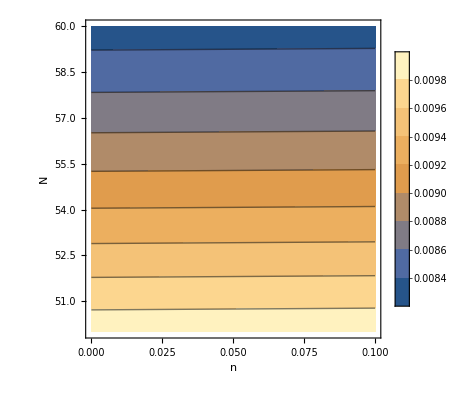

```mathematica
α=0.0014;
Clear[n,N0]
ContourPlot[Evaluate[ns[φ]/.φ->φi],{n,0,4},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"},PlotRange->{0.9646-0.0042,0.9649+0.0042}]
ContourPlot[Evaluate[nt[φ]/.φ->φi],{n,0,4},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"}]
ContourPlot[Evaluate[r[φ]/.φ->φi],{n,0,4},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"}]
N0=60;Clear[α]
ContourPlot[Evaluate[ns[φ]/.φ->φi],{n,0,4},{α,0.0001,0.1},PlotLegends->True,FrameLabel->{"n","α"},PlotRange->{0.9646-0.0042,0.9649+0.0042}]
ContourPlot[Evaluate[nt[φ]/.φ->φi],{n,0,4},{α,0.0001,0.1},PlotLegends->True,FrameLabel->{"n","α"},PlotRange->{0,0.064}]
ContourPlot[Evaluate[r[φ]/.φ->φi],{n,0,4},{α,0.0001,0.1},PlotLegends->True,FrameLabel->{"n","α"}]
n=0.999;Clear[N0]
ContourPlot[Evaluate[ns[φ]/.φ->φi],{α,0.0001,0.1},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"},PlotRange->{0.9646-0.0042,0.9649+0.0042}]
ContourPlot[Evaluate[nt[φ]/.φ->φi],{α,0.0001,0.1},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"}]
ContourPlot[Evaluate[r[φ]/.φ->φi],{α,0.0001,0.1},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"}]
```

### 3.2. Swampland Criteria.

Before proceeding, always remember that the Swampland criteria are not affected by the Chern-Simons terms since it affects only tensor perturbations. It does not influence even the evolution of the inflaton with respect to time! So the criteria for a canonical scalar potential are universal with respect to the e-folding number N and the amplitude V1 of the potential. Hence, if the criteria are not in agreement with the scalar spectral index, there is nothing we can do however if they are not in agreement with the tensor-to-scalar ratio and the tensor spectral index, one can manipulate the Chern-Simons term to obtain a viable description. Since in most cases the scalar spectral index seems to not be in agreement with the third Swampland criterion, it would be worth examining how one can affect scalar perturbations, and the easiest ways possible would be to either introduce a non-minimal coupling between the scalar field and the Ricci scalar (it should not be irrational as the Chern-Simons coupling is already a coupling between curvature and the scalar field) or introduce something new in the kinetic term, for instance add a higher order kinetic term, make the theory k-essence, add an exotic term such as Dirac-Born-Infeld and so on. It would just be more perplexed, and the theory at hand is already “too much” since it has an f(R) term which just produces this α prefactor. in the early universe via Taylor. The non-minimal coupling should perhaps be considered in a future work.

  
The first criterion is satisfied either for a small α and arbitrary exponent of the scalar potential, or arbitrary prefactor α but small exponent (roughly speaking below 1/10)

(n √α)/(√2 κ)-(√(120 n α+(n^2 α)/2))/κ

(n √α)/(√2)-√(120 n α+(n^2 α)/2)

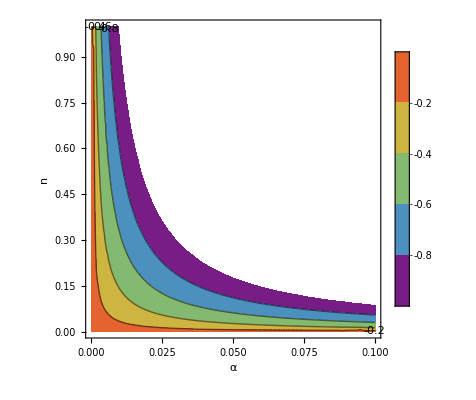

```mathematica
Clear[α,φ1,V1,Λ1,n,κ,p]
Δφ=φf-φi
  Clear[α,φ1,V1,Λ1,n,κ,p]
  N0=60; 
 κ=1;
Δφ=φf-φi
ContourPlot[Δφ,{α,0,0.1},{n,0,1},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{-1,1}]
(*Successful result. The bounds can be found quite easily*)
```

Now the second criterion can be valid for a wide variety so it does not pose a problem. It needs no consideration.

n (120 n α+(n^2 α)/2)^(1/2 (-1+n)-n/2) κ

Abs[n (120 n α+(n^2 α)/2)^(1/2 (-1+n)-n/2)]

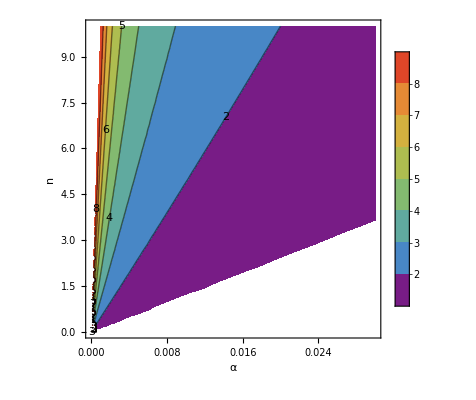

```mathematica
Clear[α,φ1,V1,Λ1,n,κ,p]
V'[φi]/V[φi]
V'[φi]/V[φi]/.{n->0.999,α->0.0014};
Clear[α,φ1,V1,Λ1,n,κ,p]
κ=1;
N0=60;
Abs[V'[φi]/V[φi]]
ContourPlot[Abs[V'[φi]/V[φi]],{α,0,0.03},{n,0,10},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{1,9}]
(*Satisfied! Nice result, easy to find the bounds*)
```

Finally, the third criterion can be satisfied for quite small values of α but the exponent must be lesser than unity. This is quite interesting and keep in mind that is independent of the Chern-Simons scalar coupling functions since now such parameter participates in the EoMs or the first slow-roll index.

-(-1+n) n (120 n α+(n^2 α)/2)^(1/2 (-2+n)-n/2)

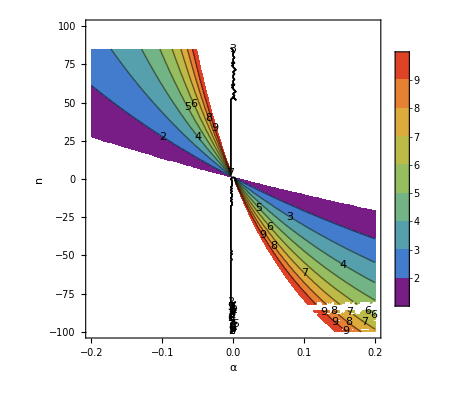

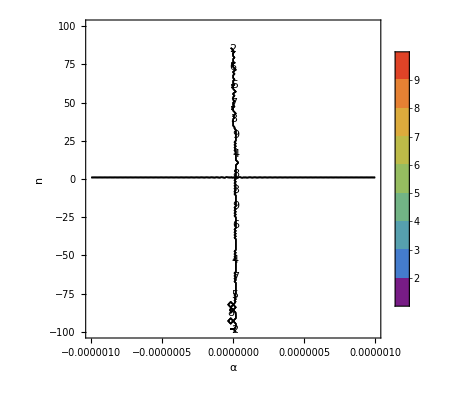

```mathematica
-V''[φi]/V[φi]/.{n->0.999,α->0.0014};
Clear[Λ];Clear[V2];Clear[N0];Clear[m];Clear[p];Clear[α];Clear[κ]; Clear[n]
κ=1;
N0=60;
-V''[φi]/V[φi]
ContourPlot[-V''[φi]/V[φi],{α,-0.2,0.2},{n,-100,100},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{1,10}]
(*Satisfied but NOT Elegant. We could find proper values for the free parameters to have an optically beautiful result and thus we zoom into the  area α->+-0*)
ContourPlot[-V''[φi]/V[φi],{α,-10^(-6),10^(-6)},{n,-100,100},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{1,10}]
(*We have values that are extremely close to m,α->+-0*)
```

### 3.3. Ascertaining The Validity Of The Approximations.

The numerical values of the slow-roll indices during the first horizon crossing according to Planck 2018 data must be of order O(10^-3) and lesser. Such results are indicative of the validity of the slow-roll approximations. Slow-roll index ε6 is excluded in this case.

```mathematica
ε1[φ]/.φ->φi//N;
ε2[φ]/.φ->φi//N;
ε6[φ]/.φ->φi//N;
```

Such result is also expected to apply on the self check on the equations of motion.

```mathematica
Hdot[φ]/.φ->φi//N;
H2[φ]/.φ->φi//N;
φdot[φ]^2/2/.φ->φi//N;
V[φ]/.φ->φi//N;
D[φdot[φ],φ]φdot[φ]/.φ->φi//N;
H[φ]φdot[φ]/.φ->φi//N;
```

## 4. Diagrammatic Results.

In this section, it is interesting to examine the area of values for certain auxiliary parameters that result in both a compatible with the observations result and also a blue shifted tensor spectral index.

```mathematica
Clear[V1];Clear[α]; Clear[α,φ1,V1,κ,N0,Mp,Λ1,p]
κ=1;
N0=60;
nt[φ];
r[φ];
ns[φ];
```

The scalar spectral index as shown is quite interesting. It behaves as if α=0.55 and n=1 are separatrixes. The elegant compatibility of the quadratic model is affected due to the rescaling. Now, n<1 seems more appropriate if one wishes to obtain compatible with the observations results while also respecting the Swampland criteria. Note that this is for N=60. Also, there exists no overlap between the pairs (α,φ1) for the scalar spectral index and the third criterion, meaning that the third cannot be satisfied properly but only loosely. 
Furthermore, the tensor spectral index can be blue tilted for p>=2 which is a really interesting result.

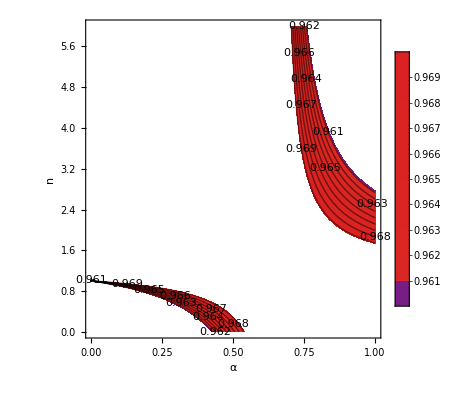

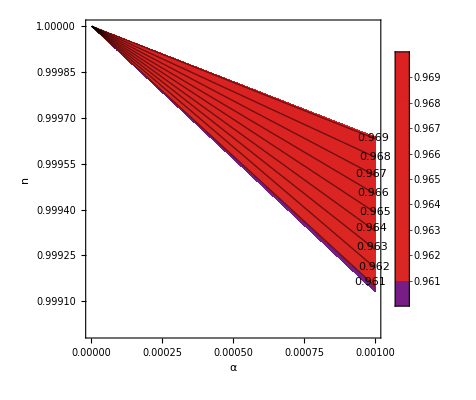

```mathematica
ContourPlot[1-2 (-((-1+n) n)/(120 n α+(n^2 α)/2)+(3 n^2 α)/(2 (120 n α+(n^2 α)/2))),{α,0,1},{n,0,6},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0.9607,0.9691}]
ContourPlot[ns[φ]/.φ->φi,{α,0,0.001},{n,0.999,1},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0.9607,0.9691}]
```

```mathematica
κ=1/Mp;Mp=1; Λ1=1;V1=Mp^4;N0=60.;n=0.9996;p=2;α=0.0006;
Δφ//N
ns[φ]/.φ->φi//N
r[φ]/.φ->φi//N
nt[φ]/.φ->φi//N
V'[φ]/(κ V[φ])/.φ->φi//N
-V''[φ]/(κ^2V[φ])/.φ->φi//N
```

-0.251519

0.964049

0.000111073

0.0082955

3.7183

0.00553251

4 Abs[(n^2 α)/(120 n α+(n^2 α)/2)] (α/Abs[α-2/3 n (120 n α+(n^2 α)/2)^(1/2 (-1+n))]+α/Abs[α+2/3 n (120 n α+(n^2 α)/2)^(1/2 (-1+n))])

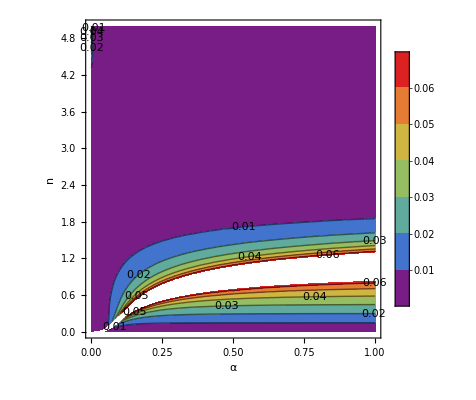

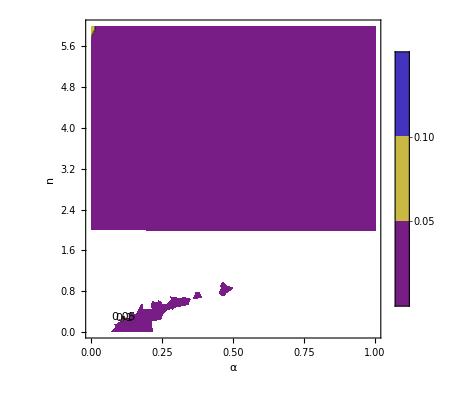

```mathematica
Clear[V1];Clear[α]; Clear[α,φ1,V1,κ,N0,Mp,Λ1,p]
κ=1;
N0=60;
Λ1=1;
V1=1;


Clear[p]
p=1;
r[φ]/.φ->φi


ContourPlot[4 Abs[(n^2 α)/(120 n α+(n^2 α)/2)] (α/Abs[α-2/3 n p (120 n α+(n^2 α)/2)^(1/2 (-2+n+p))]+α/Abs[α+2/3 n p (120 n α+(n^2 α)/2)^(1/2 (-2+n+p))]),{α,0,1},{n,0,5},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.064}]


ContourPlot[nt[φ]/.φ->φi,{α,0,1},{n,0,6},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.5}]
```

4 Abs[(n^2 α)/(110 n α+(n^2 α)/2)] (α/Abs[α-8/9 n (110 n α+(n^2 α)/2)^(1/2 (-2/3+n))]+α/Abs[α+8/9 n (110 n α+(n^2 α)/2)^(1/2 (-2/3+n))])

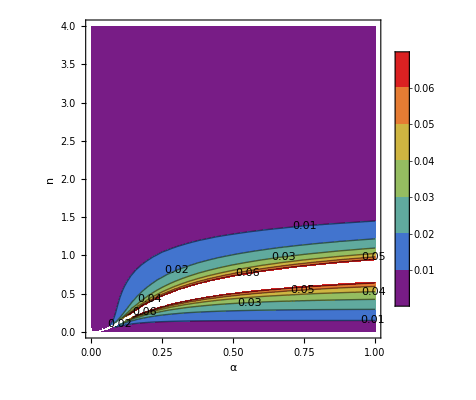

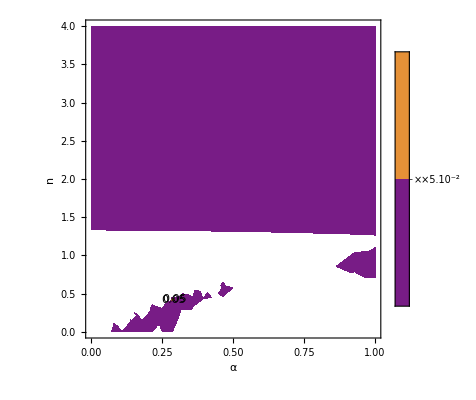

```mathematica
Clear[p]
p=4/3;
r[φ]/.φ->φi
ContourPlot[4 Abs[(n^2 α)/(120 n α+(n^2 α)/2)] (α/Abs[α-8/9 n (120 n α+(n^2 α)/2)^(1/2 (-2/3+n))]+α/Abs[α+8/9 n (120 n α+(n^2 α)/2)^(1/2 (-2/3+n))]),{α,0,1},{n,0,4},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.064}]
ContourPlot[nt[φ]/.φ->φi,{α,0,1},{n,0,4},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.5}]
```

4 Abs[(n^2 α)/(120 n α+(n^2 α)/2)] (α/Abs[α-4/3 n (120 n α+(n^2 α)/2)^(n/2)]+α/Abs[α+4/3 n (120 n α+(n^2 α)/2)^(n/2)])

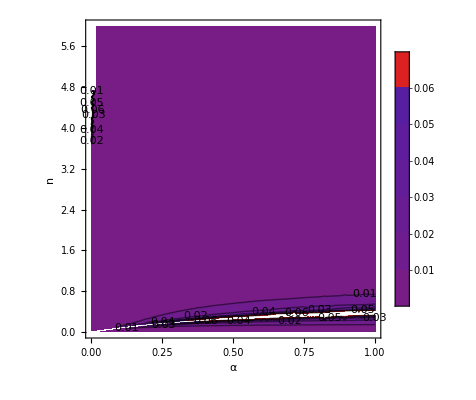

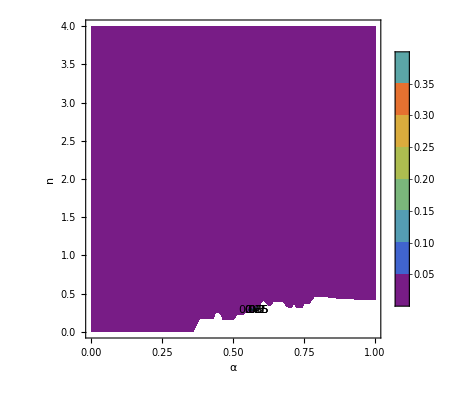

```mathematica
Clear[p]
p=2;
r[φ]/.φ->φi
ContourPlot[4 Abs[(n^2 α)/(120 n α+(n^2 α)/2)] (α/Abs[α-4/3 n (120 n α+(n^2 α)/2)^(n/2)]+α/Abs[α+4/3 n (120 n α+(n^2 α)/2)^(n/2)]),{α,0,1},{n,0,6},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.064}]
ContourPlot[nt[φ]/.φ->φi,{α,0,1},{n,0,4},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.5}]
```

4 Abs[(n^2 α)/(110 n α+(n^2 α)/2)] (α/Abs[α-2 n (110 n α+(n^2 α)/2)^((1+n)/2)]+α/Abs[α+2 n (110 n α+(n^2 α)/2)^((1+n)/2)])

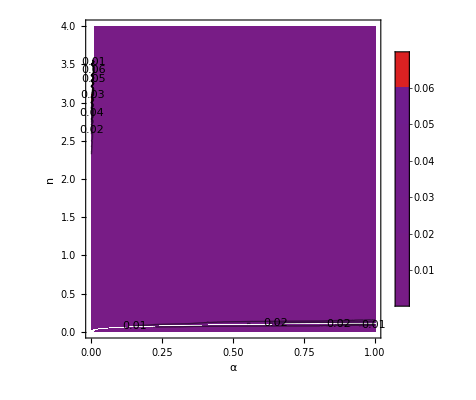

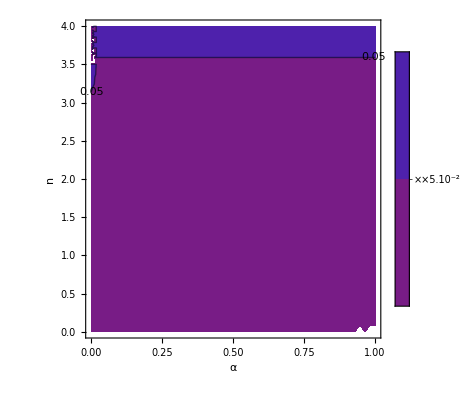

```mathematica
Clear[p]
p=3;
r[φ]/.φ->φi

ContourPlot[4 Abs[(n^2 α)/(120 n α+(n^2 α)/2)] (α/Abs[α-2 n (120 n α+(n^2 α)/2)^((1+n)/2)]+α/Abs[α+2 n (120 n α+(n^2 α)/2)^((1+n)/2)]),{α,0,1},{n,0,4},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.064}]
ContourPlot[nt[φ]/.φ->φi,{α,0,1},{n,0,4},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.5}]
```

4 Abs[(n^2 α)/(120 n α+(n^2 α)/2)] (α/Abs[α-8/3 n (120 n α+(n^2 α)/2)^((2+n)/2)]+α/Abs[α+8/3 n (120 n α+(n^2 α)/2)^((2+n)/2)])

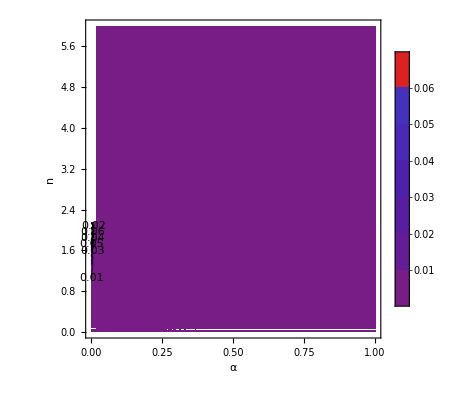

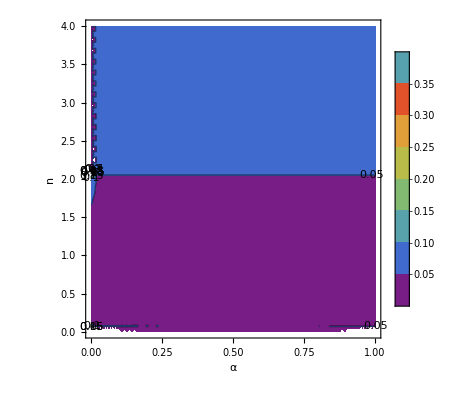

```mathematica
Clear[p]
p=4;
r[φ]/.φ->φi
ContourPlot[4 Abs[(n^2 α)/(120 n α+(n^2 α)/2)] (α/Abs[α-8/3 n (120 n α+(n^2 α)/2)^((2+n)/2)]+α/Abs[α+8/3 n (120 n α+(n^2 α)/2)^((2+n)/2)]),{α,0,1},{n,0,6},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.064}]
ContourPlot[nt[φ]/.φ->φi,{α,0,1},{n,0,4},FrameLabel->{"α","n"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.5}]
```

```mathematica
Clear[p]
r[φ]/.φ->φi
nt[φ]/.φ->φi
```

4 Abs[(n^2 α)/(110 n α+(n^2 α)/2)] (α/Abs[α-2/3 n p (110 n α+(n^2 α)/2)^(1/2 (-2+n+p))]+α/Abs[α+2/3 n p (110 n α+(n^2 α)/2)^(1/2 (-2+n+p))])

-2 ((n^2 α)/(2 (110 n α+(n^2 α)/2))+(n^2 p (-2+n+p) α (110 n α+(n^2 α)/2)^(1/2 (-4+n+p)))/(3 (α-2/3 n p (110 n α+(n^2 α)/2)^(1/2 (-2+n+p))))-(n^2 p (-2+n+p) α (110 n α+(n^2 α)/2)^(1/2 (-4+n+p)))/(3 (α+2/3 n p (110 n α+(n^2 α)/2)^(1/2 (-2+n+p)))))

The scalar spectral index is independent of the Chern-Simons scalar coupling function thus for the quadratic model, only the e-folding number affects its value. Other exponents for the scalar potential are also plausible however they must reside near the value of n=2 in order to be in agreement with experiments.

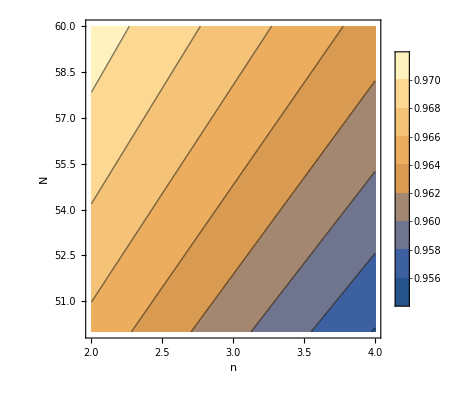

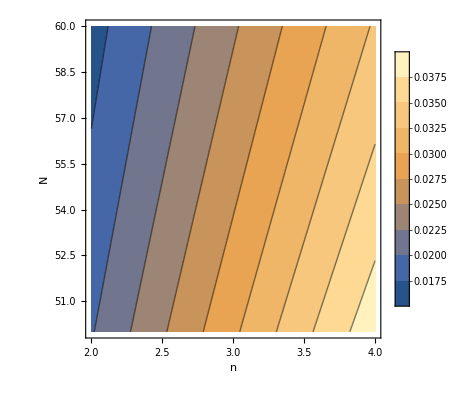

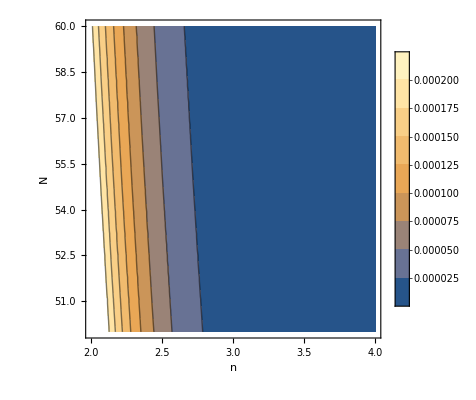

```mathematica
Clear[n];Clear[N0];V1=1;α=0.8;
ContourPlot[Evaluate[ns[φ]/.φ->φi],{n,2.,4.},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"}]
ContourPlot[Evaluate[nt[φ]/.φ->φi],{n,2.,4.},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"}]
ContourPlot[Evaluate[r[φ]/.φ->φi],{n,2.,4.},{N0,50.,60.},PlotLegends->True,FrameLabel->{"n","N"}]
```